# O3: Snell’s Law and the Index of Refraction

## Priyanka Makin Maya Fabrikant 10/13/2016

## Introduction

In this lab we explored the reflection and refraction of light through Lucite and Snell’s Law. Light is refracted from its original path when it passes from one medium to another. Snell’s Law quantifies this phenomenon and states n,,,_1*sin(θ_1) = n_2*sin(θ_2), where n_1 and n_2 are the indices of refraction for the two mediums. We also analyzed the dispersion of light which is when white light passes through a medium and is separated into its component colors. Then we can see a whole spectrum of colors, or a rainbow.

## Part 1: Index of Refraction of Lucite/Glass

1.50661

0.00509057

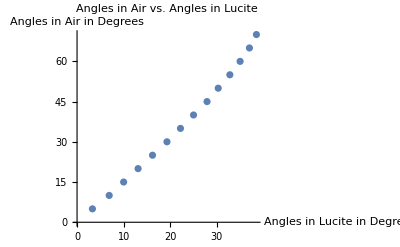

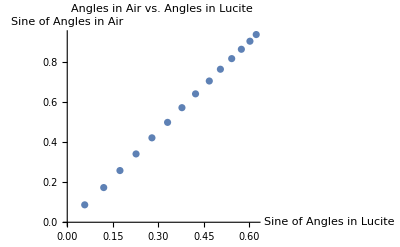

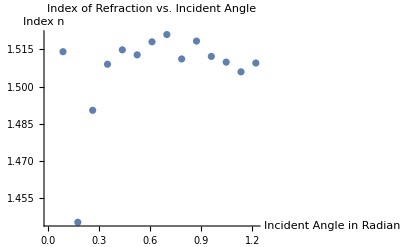

```mathematica
θadeg = {5, 10, 15, 20, 25, 30, 35, 40, 45, 50, 55, 60, 65, 70}; (*Air Angles in Degrees*)
θpdeg = {3.3, 6.9, 10, 13.1, 16.2, 19.3, 22.2, 25, 27.9, 30.3, 32.8, 35, 37, 38.5}; (*Plastic Angels in Degrees*)

θarad= θadeg * (π/180); (*Air Angles in Radians*)
θprad = θpdeg * (π/180); (*Plastic Angles in Radians*)
n = Sin[θarad]/Sin[θprad]; (*Index of Refraction*)

navg = (∑_(i=1)^Length[n] n[[i]])/Length[n] (*Average n*)
nstv = √((∑_(i=1)^Length[n] (n[[i]] - navg)^2)/(Length[n] - 1));
nsdom = nstv/√Length[n](*Uncertainty on n*)

θavsθp = Thread[{θpdeg, θadeg}];
SinθavsSinθp = Thread[{Sin[θprad], Sin[θarad]}];
nvsθa = Thread[{θarad, n}];

ListPlot[θavsθp, PlotLabel->"Angles in Air vs. Angles in Lucite", AxesLabel->{"Angles in Lucite in Degrees", "Angles in Air in Degrees"}]
ListPlot[SinθavsSinθp, PlotLabel->"Angles in Air vs. Angles in Lucite", AxesLabel->{"Sine of Angles in Lucite", "Sine of Angles in Air"}]
ListPlot[nvsθa, PlotLabel->"Index of Refraction vs. Incident Angle", AxesLabel->{"Incident Angle in Radians", "Index n"}(*,PlotRange->{0,1.6}*)]
```

Hence the measured index of refraction of lucite is 1.507 ± 0.005. I think the quality of the data we collected for this part of the lab is pretty good. As we can see, the measured index of refraction has a relatively small uncertainty associated with it. Also, the graph that compares the angles in air and in the lucite in radians seems pretty linear. In addition, the last graph compares two things that are not at all dependent on each other, so if we were to change the range of the y-axis to go from 0-1.6 we would see a horizontal line at approximately 1.51.

## Part 2: Dispersion of Lucite/Glass

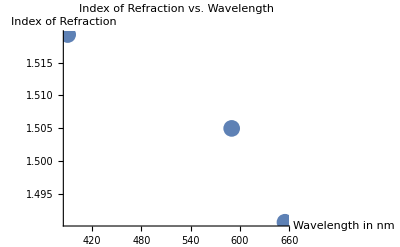

```mathematica
θp2deg = {41, 39.5, 41.5}; (*Incident Angle in Degrees*)
θReddeg = {77, 72.1, 81}; (*Red Refracted Band in Degrees*)
θViodeg = {85.9, 76.5, 89}; (*Violet Refrected Band in Degrees*)

θp2rad = θp2deg*(π/180); (*Incident Angle in Radians*)
θRedrad = θReddeg * (π/180); (*Red Refracted Band in Radians*)
θViorad = θViodeg * (π/180); (*Violet Refracted Band in Radians*)

nred = Sin[θRedrad]/Sin[θp2rad]; (*Index for Red Light*)
nvio = Sin[θViorad]/Sin[θp2rad]; (*Index for Violet Light*)

nravg = (∑_(i=1)^Length[nred] nred[[i]])/Length[nred]; (*Average Index for Red Light*)
nvioavg = (∑_(i=1)^Length[nvio] nvio[[i]])/Length[nvio]; (*Average Index for Violet Light*)
nyellow = (nravg + nvioavg)/2; (*Average INdex for Yellow Light*)

nvsλ = {{390, nvioavg}, {590, nyellow}, {655, nravg}}; (*n vs. Wavelength (nm) Data*)
ListPlot[nvsλ, PlotLabel->"Index of Refraction vs. Wavelength", AxesLabel->{"Wavelength in nm", "Index of Refraction"}, PlotStyle->PointSize[0.03]]
```

I’m not sure excatly what kind of data I was supposed to get but the information that the graph displays makes sense. If n = (speed in vaccuum)/(speed in material), as n decreases it is logical that the speed in the material (or the wavelength) must increase because the speed of the wave in vaccuum is a constant.

## Conclusion

This lab was very helpful in helping me understand the properties of light and seeing Snell’s Law in action. I think we were quite accurate with our measurements. Some precision could have been lost in our own inaccuracy of reading the correct angles, but overall our data satisfies Snell’s Law and the properties of refracted light.